# BigWham Verifications - 3DT0 Kernel

## Penny-shaped crack under uniform and shear loading

## Load Library

```mathematica
PacletDirectoryLoad[NotebookDirectory[]<>"../../../../"]
<<BigWhamLink`
GetFilesDate[]
```

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/}

BigWhamLink`LTemplate`Classes`

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Tue 25 May 2021 12:25:46GMT+2,/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a→Wed 13 Oct 2021 12:14:45GMT+2}

## Mesh

### Mesh NDSolve FEM

ToElementMesh::femtembmqg: The value, 30, for the option "MeshQualityGoal" should be a number between 0 and 1.

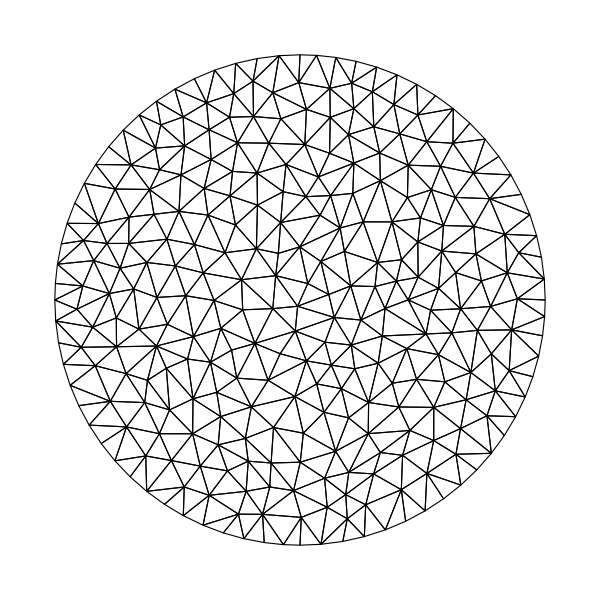

Number of Elements:512

```mathematica
Needs["NDSolve`FEM`"]
R=1;
maxCellMeasure=0.01;
Ω=Disk[{0,0},R];
mesh=ToElementMesh[Ω,"MeshOrder"->1,MaxCellMeasure->maxCellMeasure,"MaxBoundaryCellMeasure"->.1,"NodeReordering"->True,MeshQualityGoal->30];
coorVerticesXY=mesh["Coordinates"];
coorVerticesXYZ=MapThread[Append,{coorVerticesXY,ConstantArray[0,Length[coorVerticesXY]]}];
conn=mesh["MeshElements"][[1]][[1]];
Show[Graphics[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXY,Polygon[conn]]}]]
numberElements=Dimensions[conn,1][[1]];
Labeled["Number of Elements:",numberElements]
```

```mathematica
(* --- for verifications in the main.cpp --- *)
Export[NotebookDirectory[]<>"vertices.csv",coorVerticesXYZ,"CSV"]
Export[NotebookDirectory[]<>"conn.csv",conn-1,"CSV"]
```

/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/BigWhamLink/Examples/StaticCrackBenchmarks/vertices.csv

/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/BigWhamLink/Examples/StaticCrackBenchmarks/conn.csv

## Mesh utilities

### Rotation matrices

```mathematica
computeRotationMatrix[y1_List,y2_List,y3_List]:=Module[
{tangent1,normal,tangent2,rotMat},
tangent1=y2-y1;
tangent1=tangent1/Norm[tangent1];
normal=Cross[tangent1,y3-y1];
normal=normal/Norm[normal];
tangent2=Cross[normal,tangent1];
rotMat={tangent1,tangent2,normal}
];

allRotMat=Table[
computeRotationMatrix[
coorVerticesXYZ[[conn[[i,1]]]],
coorVerticesXYZ[[conn[[i,2]]]],
coorVerticesXYZ[[conn[[i,3]]]]],
{i,numberElements}];
```

## Build H-mat

```mathematica
ker="3DT0";
G=1;ν=0.25;Young=2G(1+ν);λ=(Young ν)/((1+ν)(1-2 ν));
maxleaf=50;
eta=5.;
eps=0.0001;
```

```mathematica
h1=toHMatExpr[coorVerticesXYZ,conn,ker,{Young,ν},maxleaf,eta,eps];//AbsoluteTiming
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

destructor called

{0.919647,Null}

```mathematica
GetCompressionRatio[h1]
GetSize[h1]
numberUnknowns=GetSize[h1][[1]]
numberCollocationPoints=numberUnknowns/3
```

0.760529

{1536,1536}

1536

512

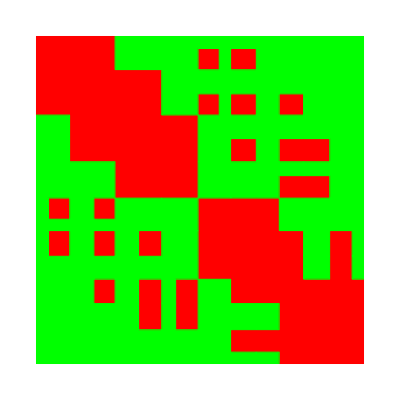

```mathematica
PlotHpattern[h1]
```

## Verification

### Compute coordinates of nodes (DD) and collocation points (traction)

#### Nodes for 3DT0

```mathematica
(* --- coordinates of nodes for 3DT0 --- *)

coorNodesXYZ=Table[
(coorVerticesXYZ[[conn[[i,1]]]]+coorVerticesXYZ[[conn[[i,2]]]]+coorVerticesXYZ[[conn[[i,3]]]])/3,
{i,numberElements}];
```

#### Collocation points

```mathematica
(* --- collocation points for any kernel --- *)

coorCollXYZ=GetCollocationPoints[h1];
```

```mathematica
allRotMat//Dimensions
```

{512,3,3}

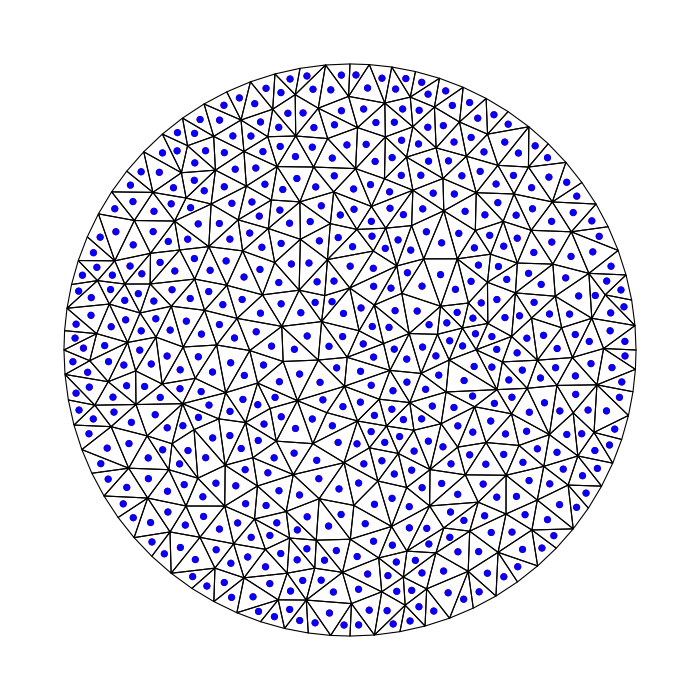

```mathematica
Show[Graphics[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXYZ[[;;,1;;2]],Polygon[conn]]}],
ListPlot[coorCollXYZ[[;;,1;;2]],PlotStyle-> Red],
ListPlot[coorNodesXYZ[[;;,1;;2]],PlotStyle-> Blue],
ImageSize-> 700]
```

## Analytical solution

#### Select direction of loading

```mathematica
comp=3;(*{1,2,3}={shear1,shear2,normal}*)
```

#### Radial coordinate of nodes (DD) and collocation points

```mathematica
rNodes=Norm[#]&/@coorNodesXYZ[[;;,1;;2]];
(*rColl=Norm[#]&/@coorCollXYZ[[;;,1;;2]];*)
rColl=Norm[#]&/@coorCollXYZ[[;;,1;;2]];
```

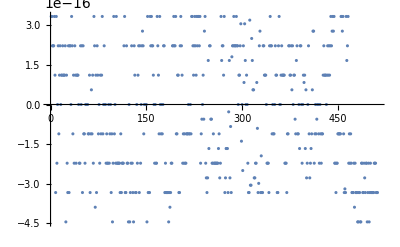

```mathematica
ListPlot[rNodes-rColl,PlotRange->All]
```

#### Analytical solutions functions

```mathematica
P=1; (*Uniform stress magnitude*)
DDsneddon[r_]:=(8 P)/(π (Young/(1-ν^2))) √Abs[R^2-r^2];
DDsegedin[r_]:=(8 (λ+2G) P)/(π G(3 λ+4G)) √Abs[R^2-r^2];

DDanalytical=ConstantArray[0.,numberUnknowns];

If[comp==3,
DDanalytical[[3;;-1;;3]]=DDsneddon[#]&/@rNodes,
DDanalytical[[comp;;-1;;3]]=DDsegedin[#]&/@rNodes];
```

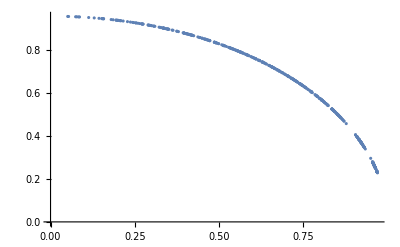

```mathematica
ListPlot[{rNodes,DDanalytical[[comp;;-1;;3]]}//Transpose]
```

```mathematica
(* --- express in local coordinate system if needed --- *)

(*for 3DT0*)

DDlocal=Table[
allRotMat[[i]].DDanalytical[[3*(i-1)+1;;3*(i-1)+3]]
,{i,numberCollocationPoints}]//Flatten;
DDanalytical=DDlocal;
```

### Test H-dot only

```mathematica
tractionNumerical=Hdot[h1,DDanalytical];//RepeatedTiming
```

{0.000343606,Null}

```mathematica
HdotRec[h1,DDanalytical];//RepeatedTiming
```

{0.000207331,Null}

```mathematica
(* --- express in global coordinate system if needed --- *)

(*for 3DT0*)

tractionGlobal=Table[
Transpose@allRotMat[[i]].tractionNumerical[[3*(i-1)+1;;3*(i-1)+3]]
,{i,numberCollocationPoints}]//Flatten;
tractionNumerical=tractionGlobal;
```

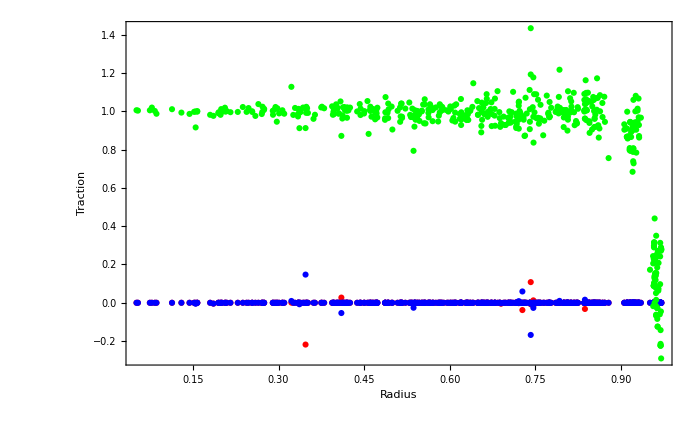

```mathematica
Show[
ListPlot[{rColl,tractionNumerical[[1;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Red],
ListPlot[{rColl,tractionNumerical[[2;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Blue],
ListPlot[{rColl,tractionNumerical[[3;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Green],
Frame-> True,BaseStyle->{FontColor->Black,FontSize->22,FontFamily->"Times"},
FrameLabel->(Style[#,FontColor->Black,FontSize->25]& /@{"Radius","Traction"}), 
PlotRange-> All,ImageSize-> 700
]
```

### Test linear solve with H-dot

```mathematica
F=ConstantArray[0.,numberUnknowns];
F[[comp;;-1;;3]]=P;
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
```

```mathematica
(* --- express in local coordinate system if needed --- *)

(*for 3DT0*)

Flocal=Table[
allRotMat[[i]].F[[3*(i-1)+1;;3*(i-1)+3]]
,{i,numberCollocationPoints}]//Flatten;
F=Flocal;
```

```mathematica
{sol,stats}=Reap@LinearSolve[fdot,F,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-5.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];//AbsoluteTiming
```

{0.017551,Null}

```mathematica
(* --- express in global coordinate system if needed --- *)

(*for 3DT0*)

solGlobal=Table[
Transpose@allRotMat[[i]].sol[[3*(i-1)+1;;3*(i-1)+3]]
,{i,numberCollocationPoints}]//Flatten;
sol=solGlobal;
```

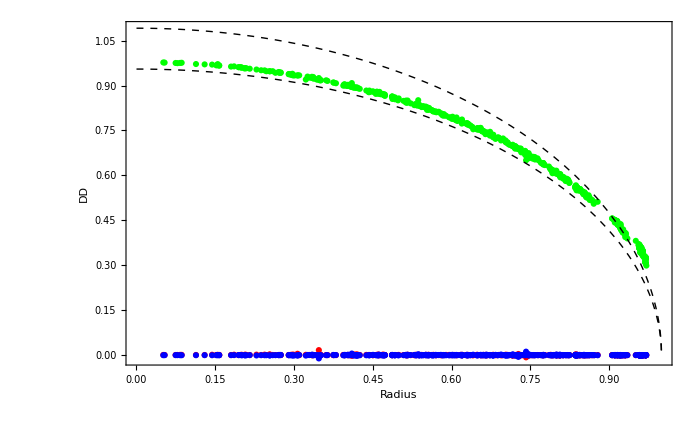

```mathematica
Show[
ListPlot[{rNodes,sol[[1;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Red],
ListPlot[{rNodes,sol[[2;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Blue],
ListPlot[{rNodes,sol[[3;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Green],
Plot[DDsneddon[x],{x,0,1},PlotStyle-> {Black,Dashed,Thick}],
Plot[DDsegedin[x],{x,0,1},PlotStyle-> {Black,Dashed,Thick}],
Frame-> True,BaseStyle->{FontColor->Black,FontSize->22,FontFamily->"Times"},
FrameLabel->(Style[#,FontColor->Black,FontSize->25]& /@{"Radius","DD"}), 
PlotRange-> All,ImageSize-> 700]
```

### Test compute stress at arbitrary points

#### For shear mixed mode (reproducing Fata’s report figures)

Note: Fata does not specify the Poisson’s ratio he used, it looks like ~0.25

```mathematica
DDsneddon[r_,P_]:=(8 P)/(π (Young/(1-ν^2))) √Abs[R^2-r^2];
DDsegedin[r_,P_]:=(8 (λ+2G) P)/(π G(3 λ+4G)) √Abs[R^2-r^2];

DDanalytical=ConstantArray[0.,numberUnknowns];

DDanalytical[[1;;-1;;3]]=DDsegedin[#,1.]&/@rNodes;
DDanalytical[[2;;-1;;3]]=DDsegedin[#,0.5]&/@rNodes;
(*DDanalytical[[3;;-1;;3]]=DDsneddon[#,1.]&/@rNodes;*)
```

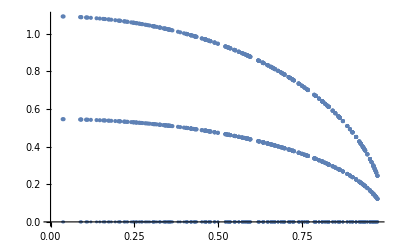

```mathematica
Show[
ListPlot[{rNodes,DDanalytical[[1;;-1;;3]]}//Transpose],
ListPlot[{rNodes,DDanalytical[[2;;-1;;3]]}//Transpose],
ListPlot[{rNodes,DDanalytical[[3;;-1;;3]]}//Transpose]
]
```

```mathematica
(* --- observation points, as in Fata's report --- *)
obs={#,0.5,1.0}&/@Range[-1.,1.,0.1]
```

{{-1.,0.5,1.},{-0.9,0.5,1.},{-0.8,0.5,1.},{-0.7,0.5,1.},{-0.6,0.5,1.},{-0.5,0.5,1.},{-0.4,0.5,1.},{-0.3,0.5,1.},{-0.2,0.5,1.},{-0.1,0.5,1.},{0.,0.5,1.},{0.1,0.5,1.},{0.2,0.5,1.},{0.3,0.5,1.},{0.4,0.5,1.},{0.5,0.5,1.},{0.6,0.5,1.},{0.7,0.5,1.},{0.8,0.5,1.},{0.9,0.5,1.},{1.,0.5,1.}}

```mathematica
(* --- when DD are in global coordinate system --- *)
stressWithDDGlobal=ComputeStresses[h1,DDanalytical,obs,Length[obs],{Young,ν},coorVerticesXYZ,conn,True]
```

calling compute stress function ...

finished!

{{-0.0530168,0.00222219,-0.103173,0.0218486,0.048363,-0.0527745},{-0.047018,0.00333115,-0.10881,0.0187972,0.0400155,-0.051948},{-0.0414385,0.00485465,-0.10859,0.0157646,0.0297407,-0.0489312},{-0.036502,0.00672356,-0.101719,0.0131792,0.0186884,-0.0438629},{-0.0321173,0.00882995,-0.0881437,0.0113679,0.00805697,-0.0371057},{-0.0279675,0.0110482,-0.0684735,0.0105003,-0.00114948,-0.0291476},{-0.023665,0.0132532,-0.0437651,0.0105862,-0.00825557,-0.0204928},{-0.0188977,0.0153313,-0.015279,0.0115136,-0.0129198,-0.0115771},{-0.0135166,0.017184,0.0157073,0.0131033,-0.0150497,-0.00272466},{-0.00754997,0.0187288,0.0479933,0.0151617,-0.0146842,0.00585692},{-0.00116114,0.0198976,0.0804624,0.0175203,-0.0118915,0.0140549},{0.00542842,0.0206378,0.112031,0.0200598,-0.00671046,0.0218146},{0.0120269,0.0209132,0.141579,0.0227194,0.000855231,0.0290967},{0.0185523,0.0207063,0.167884,0.0254918,0.0107863,0.0358337},{0.0250835,0.0200198,0.189619,0.0284032,0.022951,0.0418941},{0.0318624,0.0188762,0.205423,0.0314796,0.0369814,0.047061},{0.0392253,0.0173163,0.214071,0.0347016,0.0521643,0.05104},{0.0474646,0.0153962,0.214746,0.0379614,0.0674039,0.0535036},{0.0566547,0.0131865,0.207316,0.041041,0.0813137,0.0541741},{0.0665135,0.0107738,0.192529,0.0436314,0.092454,0.0529203},{0.0763819,0.00826082,0.171995,0.0453984,0.0996582,0.0498325}}

```mathematica
(* --- when DD are in local coordinate system of source elements --- *)

(*for 3DT0*)

DDlocal=Table[
allRotMat[[i]].DDanalytical[[3*(i-1)+1;;3*(i-1)+3]]
,{i,numberCollocationPoints}]//Flatten;
DDanalytical=DDlocal;


stressWithDDLocal=ComputeStresses[h1,DDanalytical,obs,Length[obs],{Young,ν},coorVerticesXYZ,conn,False]
```

calling compute stress function ...

finished!

{{-0.0530168,0.00222219,-0.103173,0.0218486,0.048363,-0.0527745},{-0.047018,0.00333115,-0.10881,0.0187972,0.0400155,-0.051948},{-0.0414385,0.00485465,-0.10859,0.0157646,0.0297407,-0.0489312},{-0.036502,0.00672356,-0.101719,0.0131792,0.0186884,-0.0438629},{-0.0321173,0.00882995,-0.0881437,0.0113679,0.00805697,-0.0371057},{-0.0279675,0.0110482,-0.0684735,0.0105003,-0.00114948,-0.0291476},{-0.023665,0.0132532,-0.0437651,0.0105862,-0.00825557,-0.0204928},{-0.0188977,0.0153313,-0.015279,0.0115136,-0.0129198,-0.0115771},{-0.0135166,0.017184,0.0157073,0.0131033,-0.0150497,-0.00272466},{-0.00754997,0.0187288,0.0479933,0.0151617,-0.0146842,0.00585692},{-0.00116114,0.0198976,0.0804624,0.0175203,-0.0118915,0.0140549},{0.00542842,0.0206378,0.112031,0.0200598,-0.00671046,0.0218146},{0.0120269,0.0209132,0.141579,0.0227194,0.000855231,0.0290967},{0.0185523,0.0207063,0.167884,0.0254918,0.0107863,0.0358337},{0.0250835,0.0200198,0.189619,0.0284032,0.022951,0.0418941},{0.0318624,0.0188762,0.205423,0.0314796,0.0369814,0.047061},{0.0392253,0.0173163,0.214071,0.0347016,0.0521643,0.05104},{0.0474646,0.0153962,0.214746,0.0379614,0.0674039,0.0535036},{0.0566547,0.0131865,0.207316,0.041041,0.0813137,0.0541741},{0.0665135,0.0107738,0.192529,0.0436314,0.092454,0.0529203},{0.0763819,0.00826082,0.171995,0.0453984,0.0996582,0.0498325}}

calling compute stress function ...

calling compute stress function ...

finished!

{0.042935,Null}

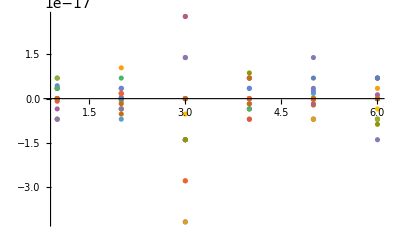

```mathematica
ListPlot[stressWithDDGlobal-stressWithDDLocal,PlotRange->All]
```

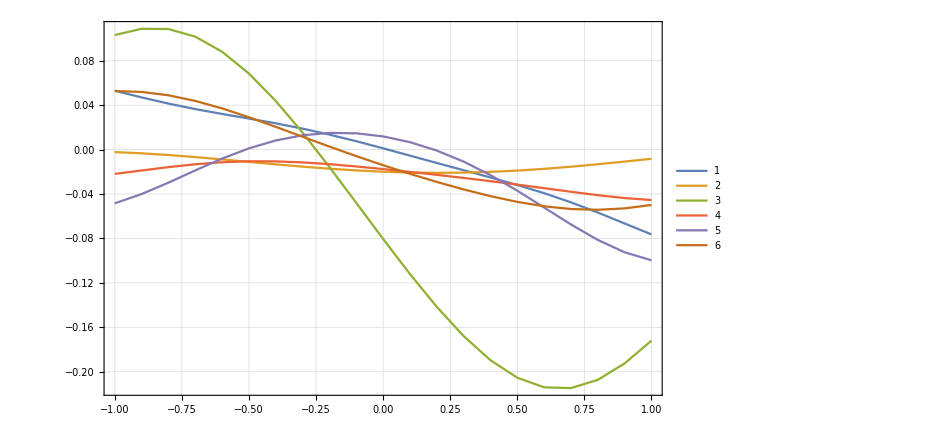

```mathematica
(* --- Fata's plot--- *)
td=TemporalData[-Transpose@stressWithDDGlobal,{obs[[;;,1]]}];
ListPlot[td,Joined->True,ImageSize->700,Frame->True,GridLines->Automatic,PlotLegends->Automatic]
```

#### For opening mode (reproducing Fata’s report figures)

Note: Fata does not specify the Poisson’s ratio he used, it looks like ~0.25

```mathematica
DDsneddon[r_,P_]:=(8 P)/(π (Young/(1-ν^2))) √Abs[R^2-r^2];
DDsegedin[r_,P_]:=(8 (λ+2G) P)/(π G(3 λ+4G)) √Abs[R^2-r^2];

DDanalytical=ConstantArray[0.,numberUnknowns];

(*DDanalytical[[1;;-1;;3]]=DDsegedin[#,1.]&/@rNodes;
DDanalytical[[2;;-1;;3]]=DDsegedin[#,0.5]&/@rNodes;*)
DDanalytical[[3;;-1;;3]]=DDsneddon[#,1.]&/@rNodes;
```

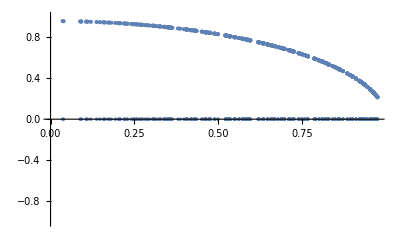

```mathematica
Show[
ListPlot[{rNodes,DDanalytical[[1;;-1;;3]]}//Transpose],
ListPlot[{rNodes,DDanalytical[[2;;-1;;3]]}//Transpose],
ListPlot[{rNodes,DDanalytical[[3;;-1;;3]]}//Transpose]
]
```

```mathematica
(* --- observation points, as in Fata's report --- *)

obs={#,0.5,1.0}&/@Range[-1.,1.,0.1]
```

{{-1.,0.5,1.},{-0.9,0.5,1.},{-0.8,0.5,1.},{-0.7,0.5,1.},{-0.6,0.5,1.},{-0.5,0.5,1.},{-0.4,0.5,1.},{-0.3,0.5,1.},{-0.2,0.5,1.},{-0.1,0.5,1.},{0.,0.5,1.},{0.1,0.5,1.},{0.2,0.5,1.},{0.3,0.5,1.},{0.4,0.5,1.},{0.5,0.5,1.},{0.6,0.5,1.},{0.7,0.5,1.},{0.8,0.5,1.},{0.9,0.5,1.},{1.,0.5,1.}}

```mathematica
(* --- when DD are in global coordinate system --- *)

stressWithDDGlobal=ComputeStresses[h1,DDanalytical,obs,Length[obs],{Young,ν},coorVerticesXYZ,conn,True]
```

calling compute stress function ...

finished!

{{0.0547895,-0.00391156,0.0623115,-0.03914,-0.1204,0.060246},{0.0471411,-0.00281055,0.100482,-0.0401406,-0.131855,0.0732928},{0.0369254,-0.0016224,0.143389,-0.039535,-0.138228,0.0864233},{0.0251808,-0.000427412,0.18866,-0.0373475,-0.138467,0.0989254},{0.0130878,0.000707286,0.233588,-0.0337855,-0.132224,0.110197},{0.001717,0.00173216,0.275562,-0.0291669,-0.119828,0.119827},{-0.00813568,0.00261267,0.312375,-0.0238324,-0.102101,0.127613},{-0.0159912,0.00332397,0.342375,-0.018077,-0.0801311,0.133524},{-0.0216336,0.00384684,0.364447,-0.0121137,-0.0550706,0.137629},{-0.0250103,0.00416637,0.377921,-0.0060691,-0.0280228,0.140034},{-0.0261343,0.00427265,0.382453,-2.28158×10^-6,-7.66082×10^-6,0.140824},{-0.0250161,0.00416225,0.377935,0.0060645,0.0280109,0.140033},{-0.0216412,0.00383881,0.364468,0.0121092,0.0550673,0.137628},{-0.0159943,0.00331246,0.342395,0.0180732,0.0801367,0.133523},{-0.00812895,0.00259825,0.312386,0.0238301,0.10211,0.127613},{0.00173466,0.0017154,0.275562,0.0291669,0.119831,0.119827},{0.0131117,0.000688547,0.233585,0.0337879,0.132214,0.110196},{0.0252021,-0.000447991,0.188665,0.0373516,0.138441,0.0989236},{0.0369357,-0.00164473,0.143416,0.03954,0.138191,0.0864203},{0.0471371,-0.0028343,0.100533,0.0401456,0.131819,0.0732888},{0.0547743,-0.00393599,0.0623831,0.0391445,0.120374,0.0602416}}

```mathematica
(* --- when DD are in local coordinate system of source elements --- *)

(*for 3DT0*)
DDlocal=Table[
allRotMat[[i]].DDanalytical[[3*(i-1)+1;;3*(i-1)+3]]
,{i,numberCollocationPoints}]//Flatten;
DDanalytical=DDlocal;

stressWithDDLocal=ComputeStresses[h1,DDanalytical,obs,Length[obs],{Young,ν},coorVerticesXYZ,conn,False]
```

calling compute stress function ...

finished!

{{0.0547895,-0.00391156,0.0623115,-0.03914,-0.1204,0.060246},{0.0471411,-0.00281055,0.100482,-0.0401406,-0.131855,0.0732928},{0.0369254,-0.0016224,0.143389,-0.039535,-0.138228,0.0864233},{0.0251808,-0.000427412,0.18866,-0.0373475,-0.138467,0.0989254},{0.0130878,0.000707286,0.233588,-0.0337855,-0.132224,0.110197},{0.001717,0.00173216,0.275562,-0.0291669,-0.119828,0.119827},{-0.00813568,0.00261267,0.312375,-0.0238324,-0.102101,0.127613},{-0.0159912,0.00332397,0.342375,-0.018077,-0.0801311,0.133524},{-0.0216336,0.00384684,0.364447,-0.0121137,-0.0550706,0.137629},{-0.0250103,0.00416637,0.377921,-0.0060691,-0.0280228,0.140034},{-0.0261343,0.00427265,0.382453,-2.28158×10^-6,-7.66082×10^-6,0.140824},{-0.0250161,0.00416225,0.377935,0.0060645,0.0280109,0.140033},{-0.0216412,0.00383881,0.364468,0.0121092,0.0550673,0.137628},{-0.0159943,0.00331246,0.342395,0.0180732,0.0801367,0.133523},{-0.00812895,0.00259825,0.312386,0.0238301,0.10211,0.127613},{0.00173466,0.0017154,0.275562,0.0291669,0.119831,0.119827},{0.0131117,0.000688547,0.233585,0.0337879,0.132214,0.110196},{0.0252021,-0.000447991,0.188665,0.0373516,0.138441,0.0989236},{0.0369357,-0.00164473,0.143416,0.03954,0.138191,0.0864203},{0.0471371,-0.0028343,0.100533,0.0401456,0.131819,0.0732888},{0.0547743,-0.00393599,0.0623831,0.0391445,0.120374,0.0602416}}

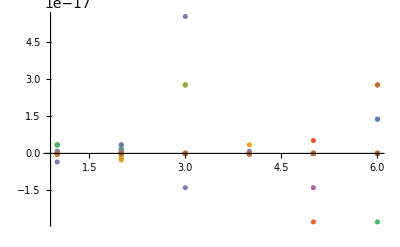

```mathematica
ListPlot[stressWithDDGlobal-stressWithDDLocal,PlotRange->All]
```

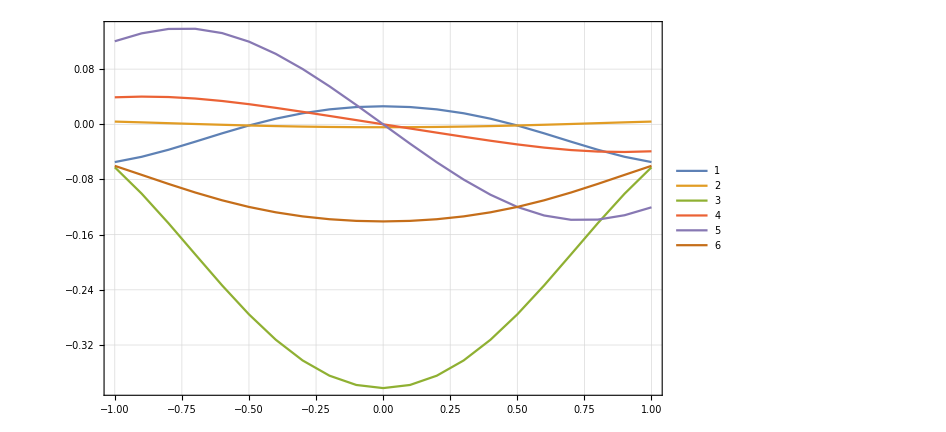

```mathematica
(* --- Fata's plot--- *)

td=TemporalData[-Transpose@stressWithDDLocal,{obs[[;;,1]]}];
ListPlot[td,Joined->True,ImageSize->700,Frame->True,GridLines->Automatic,PlotLegends->Automatic]
```